# Nerve Impulse

## Static functions and constant parameters

Functions

```mathematica
AlphaM[V_]:=
If[V≠ 25,
(0.1(25-V))/(E^((25-V)/10)-1),
1](*Limit of V=25*)

BetaM[V_]:= 4E^(-V/20)
AlphaH[V_]:=0.07E^(-V/20)
BetaH[V_]:= 1/(E^((30-V)/10)+1)
AlphaN[V_] := 
If[V≠10,
(0.01(10-V))/(E^((10-V)/10)-1),
1](*Limit of V=10*)

BetaN[V_]:=0.125E^(-V/80)
m0[V_]:=AlphaM[V]/(AlphaM[V]+BetaM[V])
Tm[V_]:=1/(AlphaM[V]+BetaM[V])
h0[V_]:=AlphaH[V]/(AlphaH[V]+BetaH[V])
Th[V_]:=1/(AlphaH[V]+BetaH[V])
n0[V_]:=AlphaN[V]/(AlphaN[V]+BetaN[V])
Tn[V_]:=1/(AlphaN[V]+BetaN[V])
```

Const

```mathematica
Gna = 120.;
```

```mathematica
Gk=34.;
```

```mathematica
Gl=0.26;
```

```mathematica
Vna=+109.;
```

```mathematica
Vk=-11.;
```

```mathematica
Vl=+11.;
```

```mathematica
V1=70.;
```

```mathematica
Plot[{m0[V],n0[V],h0[V]},{V,-100,100}, PlotLabels->"Expressions"]
```

-Graphics-

```mathematica
Plot[{Tm[V],Tn[V],Th[V]},{V,-100,100}, PlotLabels->"Expressions"]
```

-Graphics-

## Euler

Euler function

```mathematica
Euler[diff_, y0_, t0_, step_, b_] := {
numberOfSteps = Ceiling[(b-t0)/step];
ys =Array[f,numberOfSteps];
ys[[1]] = y0;
ts=Array[f,numberOfSteps];
ts[[1]] = t0;
For[i=2, i<numberOfSteps+1, i++,
ys[[i]] = ys[[i-1]] + step*diff[ts[[i-1]],ys[[i-1] ]];
ts[[i]] =  ts[[i-1]] + step;
] ;
 Transpose[{ts,ys}]
};
```

Euler Function test

```mathematica
diff[x_,y_]:=10y*(1-y)
```

```mathematica
testE := Euler [diff,0.01,0,10.0^-3,1]
```

```mathematica
s=NDSolve[{y'[x]==10y[x]*(1-y[x]) ,y[0]==0.01},y,{x,0,1}]
```

{{y→InterpolatingFunction[…]}}

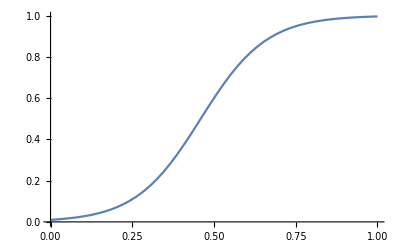

```mathematica
fPlot =Plot[y[x]/.s, {x, 0, 1}]
```

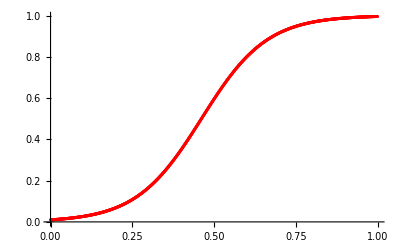

```mathematica
t1= ListPlot[testE,PlotStyle->Red]
```

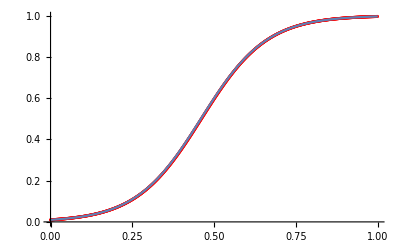

```mathematica
Show[t1,fPlot]
```

```mathematica
(*Cap := 0.91 *)
```

```mathematica
(*msolve[t_,V_]:=-((m[t]-m0[V])/Tm[V]) *)
```

```mathematica
(*hsolve[t_,V_]:=-((h[t]-h0[V])/Th[V]) *)
```

```mathematica
(*nsolve[t_,V_]:=-((n[t]-n0[V])/Tn[V]) *)
```

```mathematica
(*mhnSolve =NDSolve[ { D[m[t],t]==msolve  },m,{t,0,10}] *)
```

```mathematica
(*NDSolve[{m'[t]==msolve},m,{t,0,10}] *)
```

## m,n,h at (time zero and space x)/(time y and space 0)

Using NDSolve

```mathematica
V0=0;
```

```mathematica
NDSolve[{D[r[t],t]==0,r[0]==0},r,{t,0,10}]
```

{{r→InterpolatingFunction[…]}}

```mathematica
solN = NDSolve[{n'[t]==-((n[t]-n0[V0])/Tn[V0]),n[0]==0},n,{t,0,100}]
```

{{n→InterpolatingFunction[…]}}

```mathematica
solM=NDSolve[{m'[t]==-((m[t]-m0[V0])/Tm[V0]),m[0]==0},m,{t,0,100}]
```

{{m→InterpolatingFunction[…]}}

```mathematica
solH = NDSolve[{h'[t]==-((h[t]-h0[V0])/Th[V0]),h[0]==0},h,{t,0,100}]
```

{{h→InterpolatingFunction[…]}}

Using Euler (at different voltage)

```mathematica
V1 = 15;
V2=30;
VStart = 220;
```

```mathematica
diffM[t_,m_] :=  -((m-m0[V0])/Tm[V0])
```

```mathematica
diffN[t_,y_] :=  -((y-n0[V0])/Tn[V0])
```

```mathematica
diffH[t_,y_] := -((y-h0[V0])/Th[V0])
diffH1[t_,y_] := -((y-h0[V0])/Th[V1])
diffH2[t_,y_] := -((y-h0[V0])/Th[V2])
```

```mathematica
eulerM= Euler[diffM,0,0,0.01,1]
eulerM1:= Euler[diffM,0.5,0,0.01,1]
eulerM2:= Euler[diffM,-0.5,0,0.01,1]
```

{{{0,0},{0.01,0.00223564},{0.02,0.00437685},{0.03,0.00642763},{0.04,0.00839179},{0.05,0.010273},{0.06,0.0120747},{0.07,0.0138004},{0.08,0.0154532},{0.09,0.0170361},{0.1,0.0185522},{0.11,0.0200043},{0.12,0.0213951},{0.13,0.0227271},{0.14,0.0240028},{0.15,0.0252247},{0.16,0.0263949},{0.17,0.0275158},{0.18,0.0285892},{0.19,0.0296174},{0.2,0.0306021},{0.21,0.0315453},{0.22,0.0324486},{0.23,0.0333137},{0.24,0.0341423},{0.25,0.0349359},{0.26,0.035696},{0.27,0.036424},{0.28,0.0371213},{0.29,0.0377891},{0.3,0.0384287},{0.31,0.0390412},{0.32,0.0396279},{0.33,0.0401899},{0.34,0.0407281},{0.35,0.0412435},{0.36,0.0417372},{0.37,0.0422101},{0.38,0.0426629},{0.39,0.0430967},{0.4,0.0435121},{0.41,0.04391},{0.42,0.044291},{0.43,0.044656},{0.44,0.0450056},{0.45,0.0453404},{0.46,0.045661},{0.47,0.0459681},{0.48,0.0462623},{0.49,0.046544},{0.5,0.0468138},{0.51,0.0470723},{0.52,0.0473198},{0.53,0.0475568},{0.54,0.0477839},{0.55,0.0480013},{0.56,0.0482096},{0.57,0.0484091},{0.58,0.0486001},{0.59,0.0487831},{0.6,0.0489583},{0.61,0.0491262},{0.62,0.049287},{0.63,0.0494409},{0.64,0.0495884},{0.65,0.0497296},{0.66,0.0498649},{0.67,0.0499945},{0.68,0.0501186},{0.69,0.0502374},{0.7,0.0503512},{0.71,0.0504603},{0.72,0.0505647},{0.73,0.0506647},{0.74,0.0507605},{0.75,0.0508522},{0.76,0.0509401},{0.77,0.0510242},{0.78,0.0511048},{0.79,0.051182},{0.8,0.0512559},{0.81,0.0513267},{0.82,0.0513946},{0.83,0.0514595},{0.84,0.0515217},{0.85,0.0515813},{0.86,0.0516384},{0.87,0.051693},{0.88,0.0517454},{0.89,0.0517955},{0.9,0.0518435},{0.91,0.0518895},{0.92,0.0519336},{0.93,0.0519758},{0.94,0.0520162},{0.95,0.0520549},{0.96,0.052092},{0.97,0.0521275},{0.98,0.0521615},{0.99,0.052194}}}

```mathematica
eulerN:= Euler[diffN,0,0,0.01,30]
eulerN1:= Euler[diffN,1,0,0.01,30]
eulerN2:= Euler[diffN,-1,0,0.01,30]
```

```mathematica
eulerH:= Euler[diffH,0,0,0.01,30]
eulerH1:= Euler[diffH1,0,0,0.01,30]
eulerH2:= Euler[diffH2,0,0,0.01,30]
```

```mathematica
(*eulerH:= Euler[diffH,0,0,0.01,30]
eulerH1:= Euler[diffH,1,0,0.01,30]
eulerH2:= Euler[diffH,h0[V0],0,0.01,30]*)
```

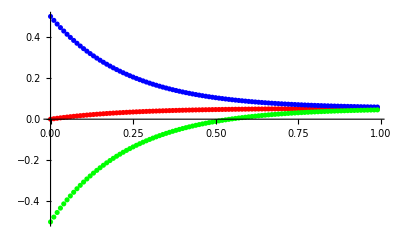

```mathematica
plotEulerM := ListPlot[eulerM, PlotStyle->Red]
plotEulerM1 := ListPlot[eulerM1, PlotStyle->Blue]
plotEulerM2 := ListPlot[eulerM2, PlotStyle->Green]
Show[{plotEulerM, plotEulerM1, plotEulerM2}, PlotRange->All]
```

```mathematica
(*Show[plotEulerM,Plot[Evaluate[ m[x]/. solM] ,{x,0,1}, PlotRange->All]]*)
```

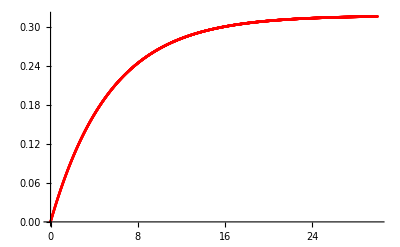

```mathematica
plotEulerN := ListPlot[eulerN, PlotStyle->Red]
plotEulerN1 := ListPlot[eulerN1, PlotStyle->Blue]
plotEulerN2 := ListPlot[eulerN2, PlotStyle->Green]
Show[{plotEulerN(*, plotEulerN1, plotEulerN2*)}]
```

```mathematica
(*Show[{ListPlot[Euler[diffN,0,0,0.01,30],PlotStyle->RGBColor[1, 0, 0]],ListPlot[Euler[diffN,1,0,0.01,30],PlotStyle->RGBColor[0, 0, 1]],ListPlot[Euler[diffN,-1,0,0.01,30],PlotStyle->RGBColor[0, 1, 0]]},PlotRange->All]*)
```

```mathematica
(*Show[plotEulerN,Plot[Evaluate[ n[x] /. solN] ,{x,0,30}]]*)
```

```mathematica
plotEulerH:= ListPlot[eulerH, PlotStyle->Red]
plotEulerH1 := ListPlot[eulerH1, PlotStyle->Blue]
plotEulerH2 := ListPlot[eulerH2, PlotStyle->Green]
```

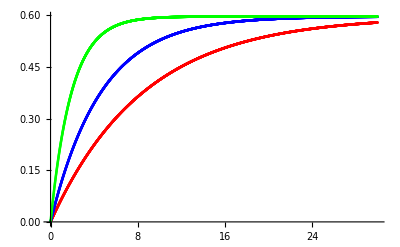

```mathematica
Show[{plotEulerH, plotEulerH1, plotEulerH2}, PlotRange->All]
```

```mathematica
(*Show[plotEulerH,Plot[Evaluate[ h[x] /. solH] ,{x,0,30}]]*)
```

```mathematica
(*Jion[t_]=(*Gna m^3h[t](V-Vna)+*)Gk n[t]^4(6-Vk)+Gl(6-Vl)*)
```

## Jion function

```mathematica
(*Evaluate[Jion [t] /. {n->solN}]*)
```

```mathematica
MakePoints[f, NPoints] = {
arr = Array
For[i= 0, i≤NPoints, i++]}
```

{Array Null}

Jion as a function of V (m=m0,n=n0,h=h0)

```mathematica
Jion1[V_]:= Gna*m0[V]^3*h0[V]*(V-Vna)+Gk* n0[V]^4(V-Vk)+Gl(V-Vl)
```

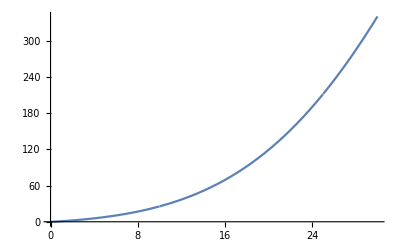

```mathematica
Plot[Jion1[V], {V,0, 30}]
```

Jion as a function of t (time) and plugging m,n,h from NDSolve (at V0)

```mathematica
Jion[t_]:= Gna*Evaluate[m[t]/.solM]^3*Evaluate[h[t]/.solH]*(V0-Vna)+Gk*Evaluate[ n[t]/.solN]^4(V0-Vk)
```

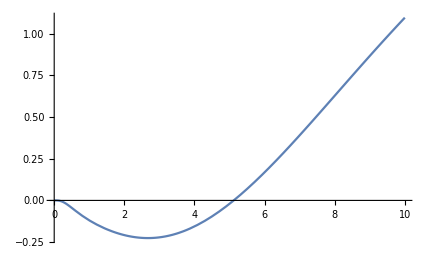

```mathematica
Plot[Jion[t],{t,0,10}, PlotRange->All]
```

Jion as a function of t (time) and plugging m,n,h from Euler (at V0)

```mathematica
Ms= eulerM[[1]];
```

```mathematica
Ns= eulerN[[1]];
```

```mathematica
Hs = eulerH[[1]];
```

```mathematica
Ms[[2,2]]
```

0.00223564

```mathematica
JionEuler[t_]:= N[Gna*  Ms[[t*100+1,2]]   ^3* Hs[[t*100+1,2] ]   *(V0-Vna)+Gk*    Ns[[t*100+1,2]]   ^4(V0-Vk)]
```

```mathematica
JionEuler[.99]
```

-0.11885

```mathematica
JionList=Table[JionEuler[i],{i,0.01,0.99,0.01}]
```

{-1.02265×10^-7,-1.53381×10^-6,-7.28222×10^-6,-0.0000215947,-0.0000494898,-0.0000963763,-0.00016776,-0.000269022,-0.000405256,-0.000581153,-0.000800926,-0.00106826,-0.00138629,-0.0017576,-0.00218422,-0.00266768,-0.00320898,-0.00380868,-0.00446692,-0.00518342,-0.00595759,-0.0067885,-0.00767497,-0.00861556,-0.00960864,-0.0106524,-0.011745,-0.0128842,-0.0140681,-0.0152943,-0.0165607,-0.0178649,-0.0192048,-0.020578,-0.0219824,-0.0234157,-0.0248757,-0.0263604,-0.0278676,-0.0293954,-0.0309419,-0.0325052,-0.0340835,-0.035675,-0.0372782,-0.0388916,-0.0405135,-0.0421426,-0.0437775,-0.0454171,-0.04706,-0.0487052,-0.0503516,-0.0519982,-0.0536441,-0.0552885,-0.0569305,-0.0585693,-0.0602044,-0.0618349,-0.0634604,-0.0650803,-0.0666941,-0.0683013,-0.0699015,-0.0714943,-0.0730794,-0.0746564,-0.0762251,-0.0777853,-0.0793366,-0.0808789,-0.082412,-0.0839358,-0.08545,-0.0869547,-0.0884497,-0.089935,-0.0914104,-0.0928759,-0.0943315,-0.0957772,-0.0972129,-0.0986387,-0.100055,-0.10146,-0.102856,-0.104242,-0.105619,-0.106985,-0.108342,-0.109689,-0.111026,-0.112354,-0.113672,-0.11498,-0.11628,-0.11757,-0.11885}

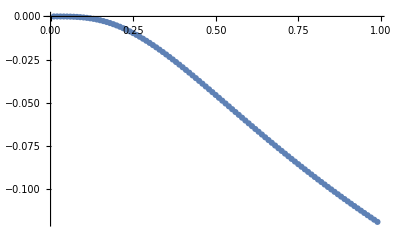

```mathematica
ListPlot[Table[{i/100,JionList[[i]]},{i,1,99}]]
```

## Legacy code

```mathematica
(*I = 0
NSolve[I - Jion[t] ]*)
```

```mathematica
(*f1 = (Gna m^3h(V-Vna)+Gk n^4(V-Vk)+Gl(V-Vl) +Iapp)/Cm *)
```

```mathematica
(*f2 = AlphaM[V]*(1- m) - BetaM[V]*m *)
```

```mathematica
(*f3 = AlphaN[V]*(1- n) - BetaN[V]*n *)
```

```mathematica
(*f4 = AlphaH[V]*(1- h) - BetaH[V]*h *)
```

```mathematica
(*NDEuler[diff_, y0_, step_, a_, b_] := {
ys = Range[a,b,step];
ys[[1]] = y0;
numberOfSteps = (b-a)/step;
For[i=2, i<numberOfSteps+2, i++,
ys[[i]] = ys[[i-1]] + step*diff[a + (i-1)*step]
] ;
ys
};*)
```

```mathematica
(*diff[x_] = 2x*)
```

```mathematica
(*list =NDEuler[diff, 1, 0.1, 0, 10]*)
```

```mathematica
(*listX = Range[0,10, 1]*)
```

```mathematica
(*lPlot = ListPlot[list]*)
```

## m , n , h and V across time and space

```mathematica
(* F/cm *)
```

```mathematica
(* ohms/cm *)
```

```mathematica
(*For[i=1, i≤100, i++,
If[voltage>0,
{VMatrix[[1, i]] = voltage[i];
MMatrix[[1, i]] =  m0[voltage[i]-0.001];
NMatrix[[1, i]] =  n0[voltage[i]-0.001];
HMatrix[[1, i]] =  h0[voltage[i]-0.001];},
{MMatrix[[1, i]] =  m0[0];
NMatrix[[1, i]] =  n0[0];
HMatrix[[1, i]] =  h0[0];
}
];
];*)
```

```mathematica
(*Mij[i_,j_ ] := MMatrix[[i,j-1]] + Te*(-(MMatrix[[i,j-1]]-m0*(VMatrix[[i,j-1]]))/Tm[VMatrix[[i,j-1]]])*)
```

```mathematica
(*Nij[i_,j_ ] := NMatrix[[i,j-1]] + Te*(-(NMatrix[[i,j-1]]-n0*(VMatrix[[i,j-1]]))/Tn[VMatrix[[i,j-1]]]);*)
```

```mathematica
(*Hij[i_,j_ ] := HMatrix[[i,j-1]] + Te*(-(HMatrix[[i,j-1]]-h0*(VMatrix[[i,j-1]]))/Th[VMatrix[[i,j-1]]]);*)
```

```mathematica
(*Vij[i_,j_]:= -Te((*Jion[lenx*i,Te*j]*) 1 - Cap* VMatrix[[i,j-1]]/Te  -1/1 * (VMatrix[[i+1,j-1]]-2* VMatrix[[i,j-1]] + VMatrix[[i-1,j-1]])/lenx^2)/Cap;*)
```

```mathematica
(*MJion[i_ , j_]:=   Gna*  MMatrix[[i,j]]  ^3* HMatrix[[i,j]]   *(VMatrix[[i,j]]-Vna)+ Gk *  NMatrix[[i,j]]   ^4(VMatrix[[i,j]]-Vk); *)
```

```mathematica
a =Table[Table[0, {i,Tmax}], {j,Xmax}];
```

```mathematica
a
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
Clear[voltage]
Clear[VMatrix](*this might not be needed*)
Clear[MMatrix](*this might not be needed*)
Clear[NMatrix](*this might not be needed*)
Clear[HMatrix](*this might not be needed*)
lenx = 0.01;
Te=0.001; 
Cap=0.91;
R=2;
Tmax=10;
Xmax=20;
VMatrix=Table[Table[0, {i,Xmax}], {j,Tmax}];
For[i = 1, i≤Tmax, i++,
VMatrix[[i,1]] = 220;
VMatrix[[i,Xmax]] = 0;
]
MMatrix = Table[Table[0, {i,Xmax}], {j,Tmax}];
NMatrix = Table[Table[0, {i,Xmax}], {j,Tmax}];
HMatrix = Table[Table[0, {i,Xmax}], {j,Tmax}];
voltage[x_]= 220 - lenx*x*1000;
For[j=1, j≤Xmax, j++,
If[voltage[j]>0,
{VMatrix[[1, j]] = voltage[j];
MMatrix[[1, j]] =  m0[voltage[j]];
NMatrix[[1, j]] =  n0[voltage[j]];
HMatrix[[1, j]] =  h0[voltage[j]];},
{MMatrix[[1, j]] =  m0[0];
NMatrix[[1, j]] =  n0[0];
HMatrix[[1, j]] =  h0[0];
}
];
];

MJion[i_,j_]:=Gna*  MMatrix[[i,j]]  ^3* HMatrix[[i,j]]   *(VMatrix[[i,j]]-Vna)+ Gk *  NMatrix[[i,j]]^4(VMatrix[[i,j]]-Vk); 

For[i=2,i< Tmax,i++,(*if not in one cell with the above code ^ it gives a underflow/overflow ereor after 1st compile*)
{
For[j=2,j<Xmax,j++,
{
VMatrix[[i, j]] =   VMatrix[[i-1,j]] + Te/Cap*(  - MJion[i,j] +   1/R*  (  VMatrix[[i-1,j+1]] -2*VMatrix[[i-1,j]] + VMatrix[[i-1,j-1]]  )/(lenx^2)  );
MMatrix[[i, j]] =   MMatrix[[i-1,j]] + Te*(-(MMatrix[[i-1,j]]-m0[VMatrix[[i-1,j]]])/Tm[VMatrix[[i-1,j]]]);
NMatrix[[i, j]] =   NMatrix[[i-1,j]] + Te*(-(NMatrix[[i-1,j]]-n0[VMatrix[[i-1,j]]])/Tn[VMatrix[[i-1,j]]]);
HMatrix[[i, j]] =   HMatrix[[i-1,j]] + Te*(-(HMatrix[[i-1,j]]-h0[VMatrix[[i-1,j]]])/Th[VMatrix[[i-1,j]]]);
}
]
}
]
```

```mathematica
VMatrix
```

{{210.,200.,190.,180.,170.,160.,150.,140.,130.,120.,110.,100.,90.,80.,70.,60.,50.,40.,30.,20.},{220,200.,190.,180.,170.,160.,150.,140.,130.,120.,110.,100.,90.,80.,70.,60.,50.,40.,30.,0},{220,254.945,190.,180.,170.,160.,150.,140.,130.,120.,110.,100.,90.,80.,70.,60.,50.,40.,-79.8901,0},{220,-293.902,491.896,180.,170.,160.,150.,140.,130.,120.,110.,100.,90.,80.,70.,60.,50.,-563.792,1017.8,0},{220,6847.3,-5539.39,1838.77,170.,160.,150.,140.,130.,120.,110.,100.,90.,80.,70.,60.,-3267.54,11498.8,-13264.6,0},{220,-97625.2,103059.,-47869.6,9284.11,160.,150.,140.,130.,120.,110.,100.,90.,80.,70.,-18168.2,96149.2,-205697.,195680.,0},{220,1.54264×10^6,-1.82888×10^6,1.09544×10^6,-354880.,50237.5,150.,140.,130.,120.,110.,100.,90.,80.,-100085.,710160.,-2.19047×10^6,3.65817×10^6,-3.08486×10^6,0},{220,-2.54571×10^7,3.27636×10^7,-2.2941×10^7,9.83982×10^6,-2.45089×10^6,275301.,140.,130.,120.,110.,100.,90.,-550223.,4.90217×10^6,-1.96792×10^7,4.58824×10^7,-6.55268×10^7,5.09145×10^7,0},{220,4.34312×10^8,-5.932×10^8,4.63243×10^8,-2.37806×10^8,8.00595×10^7,-1.62156×10^7,1.51196×10^6,130.,120.,110.,100.,-3.02355×10^6,3.24317×10^7,-1.60119×10^8,4.75612×10^8,-9.26485×10^8,1.1864×10^9,-8.68623×10^8,0},{220,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}